```mathematica
λ=1;
γ=10;
d=40;
αp=2/3;
απ1=2/3;

λ1=-Log[1-1/γ];
λ2=((d αp+γ) Log[γ/(-1+γ)])/γ;
λc=(d αp+γ)/γ;
```

```mathematica
ρp[λ_,d_,γ_,αp_]:=λ/(1+αp*d/γ);
ρpTwo[γ_]:=-Log[1-1/(γ)];
ρπ1[γ_]:=-Log[1-1/(γ)];
ρπ1Two[λ_,d_,αp_,ρp_]:=-Log[1-(λ-ρp)/(ρp*αp*d)];
ρπ2[γ_,d_,απ1_,ρp_]:=-Log[1+(1-γ*(1-Exp[-ρp]))/(απ1*d)];
```

```mathematica
Import["/home/onofrio/Dropbox/Lavoro/Predator-prey/Simulazioni/3level.dat"]
```

{{1,0.272939,0.147235,0.0467033},{1.5,0.439308,0.140379,0.0914337},{2,0.614098,0.142879,0.13024},{2.5,0.795028,0.145829,0.169088},{3,0.998747,0.147806,0.204938},{3.5,1.24123,0.151324,0.235978},{4,1.56853,0.178484,0.256955}}

```mathematica
0.14908170370370338 0.0004961111111111092
```

```mathematica
nump:={{0.15,0.14908170370370338},{0.2,0.15566684956561494},{0.25,0.14681152263374492},{0.5,0.14525390946502054},{1,0.2729390946502049},{1.5,0.43930823045267453},{2,0.6140979423868321},{2.5,0.7950283950617283},{3,0.9987469135802469},{3.5,1.2412308641975278},{4,1.5685251028806617},{5,2.261672404938269},{6,3.04989817283952},{7,3.7791417679012387},{8,4.480367190123446},{9,5.378759061728403},{12,7.3143},{15,9.3824},{17,10.5261},{20,12.8087
}}
numπ1:={{0.15,0.0004961111111111092},{0.2,0.017523639689071644},{0.25,0.037799999999999875},{0.5,0.12422716049382654},{1,0.14723497942386832},{1.5,0.1403790123456789},{2,0.1428790123456787},{2.5,0.14582880658436187},{3,0.14780617283950584},{3.5,0.1513238683127571},
{4,0.1784835390946499},{5,0.22230968888888866},{6,0.27737076543209815},{7,0.3275916543209873},{8,0.3714251950617278},{9,0.42253167407407477},{12,0.5594},{15,0.5912},{17,0.65560},{20,0.7241}}
numπ2:={{0.5,0.0013613168724279973},{1,0.04670329218107002},{1.5,0.09143374485596671},{2,0.13023950617283883},{2.5,0.16908765432098716},{3,0.20493786008230455},{3.5,0.2359781893004117},{4,0.2569551440329218},{5,0.2981263407407403},{6,0.33034032592592577},{7,0.36554466172839495},{8,0.4100187753086421},{9,0.4152869827160485},{12,0.5689},{15,0.7256},{17,0.8375},{20,0.9569}}
```

```mathematica
0.10593740740740744 0.01608444444444447
```

```mathematica
numMFp={{0.15,0.10593740740740744},{0.2,0.1070988683127573},{0.25,0.11123251028806636},{0.5,0.13472633744855922},{1,0.27396995884773684},{1.5,0.4377325102880666},{2,0.5823349794238688},{2.5,0.8004638888888905},{3,0.9671576131687237}}; 
numMFπ1={{0.15,0.01608444444444447},{0.2,0.03310997942386812},{0.25,0.04829753086419773},{0.5,0.10813127572016452},{1,0.10759218106995878},{1.5,0.109616975308642},{2,0.11327695473251033},{2.5,0.11369485596707812},{3,0.11532458847736614}};
numMFπ2={{0.5,0.009947736625514342},{1,0.05198353909465044},{1.5,0.09848189300411556},{2,0.12956625514403217},{2.5,0.17465082304526727},{3,0.19846440329218046}};
```

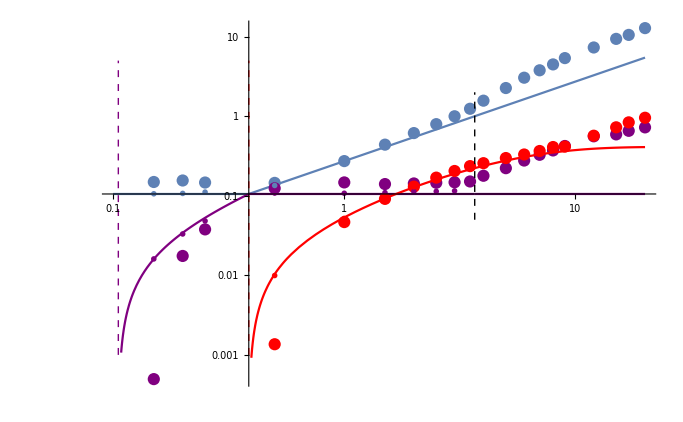

```mathematica
Show[LogLogPlot[ρp[λ, d,γ,αp],{λ,λ2,λc},PlotRange->All],LogLogPlot[ρp[λ, d,γ,αp],{λ,λc,20},PlotRange->All],LogLogPlot[ρpTwo[γ],{λ,0.1,λ2},PlotRange->All],ListLogLogPlot[nump],LogLogPlot[ρπ1[γ  ],{λ,λ2,λc},PlotRange->All,PlotStyle->Purple],LogLogPlot[ρπ1[γ  ],{λ,λc,20},PlotRange->All,PlotStyle->{Purple}],LogLogPlot[ρπ1Two[λ, d,αp,ρpTwo[γ]],{λ,λ1+0.003,λ2},PlotRange->All,PlotStyle->{Purple}],ListLogLogPlot[numπ1, PlotStyle->Purple],LogLogPlot[ρπ2[γ, d,απ1,ρp[λ, d,γ,αp ]],{λ,λ2+0.01,20},PlotRange->All,PlotStyle->Red],ListLogLogPlot[numπ2,PlotStyle->Red],ListLogLogPlot[numMFp,PlotMarkers->{"OpenMarkers"}],ListLogLogPlot[numMFπ1,PlotMarkers->{"OpenMarkers"},PlotStyle->{Purple}],ListLogLogPlot[numMFπ2,PlotMarkers->{"OpenMarkers"},PlotStyle->{Red}],ParametricPlot[{Log[λ1],x},{x,Log@0.001,Log@5},PlotStyle->{ Purple,Thick,Dashed}],ParametricPlot[{Log[λ2],x},{x,Log@0.001,Log@5},PlotStyle->{Red, Thick,Dashed}],ParametricPlot[{Log[λc],x},{x,Log@0.05,Log@2},PlotStyle->{Black, Thick,Dashed}],PlotRange->Full,PlotTheme->"Classic"]
```

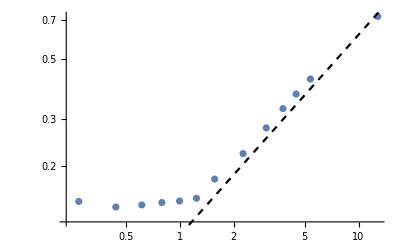

```mathematica
Show[ListLogLogPlot[{{0.2729390946502049,0.14723497942386832},{0.43930823045267453,0.1403790123456789},{0.6140979423868321,0.1428790123456787},{0.7950283950617283,0.14582880658436187},{0.9987469135802469,0.14780617283950584},{1.2412308641975278,0.1513238683127571},{1.5685251028806617,0.1784835390946499},{2.261672404938269,0.22230968888888866},{3.04989817283952,0.27737076543209815},{3.7791417679012387,0.3275916543209873},{4.480367190123446,0.3714251950617278},{5.378759061728403,0.42253167407407477},{12.8087,0.7241}},PlotRange->All],LogLogPlot[0.11x^(3/4),{x,1,15},PlotStyle->{Dashed,Black}]]
```

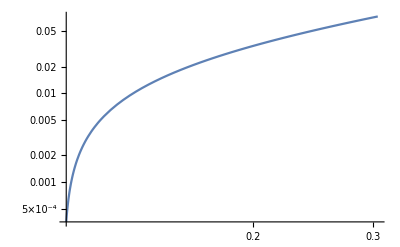

```mathematica
LogLogPlot[ρπ1Two[x,d,αp,ρpTwo[γ]],{x,λ1+0.001,λ1+0.2}]
```

Plot critical point λ1

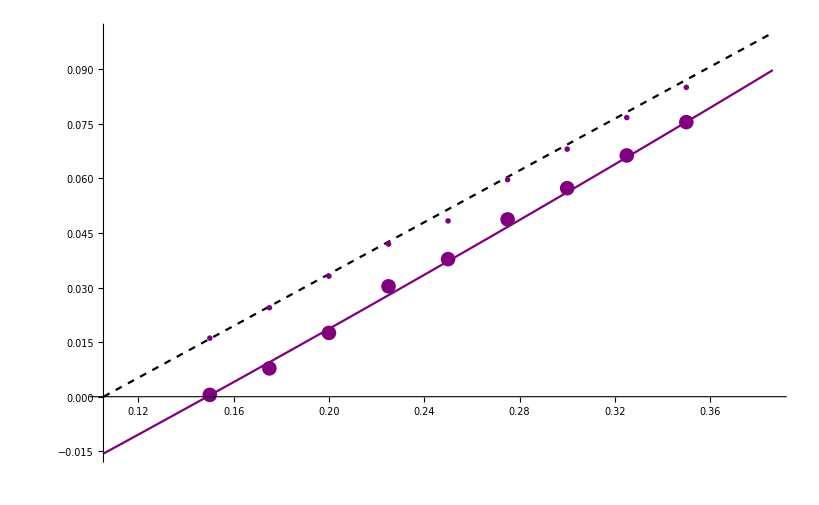

```mathematica
Show[Plot[(λ-λ1)/(αp*d*λ1),{λ,λ1,λ2},PlotStyle->{Black,Dashed}],ListPlot[{{0.15,0.0004961111111111092},{0.175,0.007783127572016453},{0.2,0.017523639689071644},{0.225,0.030320987654320876},{0.25,0.037799999999999875},{0.275,0.04871138888888878},{0.3,0.05728652263374492},{0.325,0.06628284722222146},{0.35,0.07543548611111085}},PlotStyle->Purple],ListPlot[{{0.15,0.01608444444444447},{0.175,0.02443744855967082},{0.2,0.03310997942386812},{0.225,0.04192555555555554},{0.25,0.04829753086419773},{0.275,0.059617708333333616},{0.3,0.06802201646090528},{0.325,0.07668243055555589},{0.35,0.08499340277777839}},PlotStyle->{Purple},PlotMarkers->{"OpenMarkers"}],Plot[-1/64+ρπ1Two[λ, d,αp,ρpTwo[γ]],{λ,λ1,λ2},PlotRange->All,PlotStyle->{Purple}],PlotRange->Full]
```

Plot critical point λ2

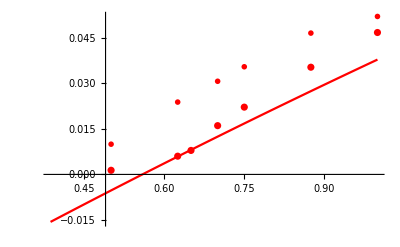

```mathematica
Show[ListPlot[{{0.5,0.0013613168724279973},{0.625,0.006002013888888972},{0.65,0.007892847222222239},{0.7,0.01604958333333331},{0.75,0.022140902777777843},{0.875,0.035279583333333295},{1,0.04670329218107002}},PlotStyle->Red],ListPlot[{{0.5,0.009947736625514342},{0.625,0.023806041666666566},{0.7,0.03065597222222217},{0.75,0.035428194444444346},{0.875,0.04651000000000001},{1,0.05198353909465044}},PlotStyle->Red,PlotMarkers->{"OpenMarkers"}],Plot[-1/64+ρπ2[γ, d,απ1,ρp[λ, d,γ,αp ]],{λ,λ2,1},PlotRange->All,PlotStyle->Red],PlotRange->Full]
```

```mathematica
N@Exp[-1/64]
```

0.984496